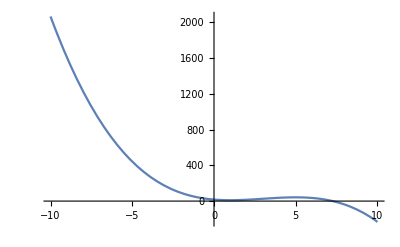

```mathematica
(*
f(x) = -x^3+9 x^2-15x+17
(a) Find the intervals in which f is increasing and is decreasing.
(b) Find the intervals in which f is concave upward and concave downward.
(c) Find the absolute maximum and absolute minimum of f if any.
*)
f[x_]=-x^3+9 x^2-15x+17;
Plot[f[x],{x,-10,10}]
```

```mathematica
Solve[f'[x]==0]
```

{{x→1},{x→5}}

```mathematica
f'[x]/.{x-> -5}
```

-180

```mathematica
(*f is decreasing on -10 to 1*)
f'[x]/.{x-> 3}
```

12

```mathematica
(*f is increasing on 1 to 5*)
```

```mathematica
f'[x]/.{x-> 9}
```

-96

```mathematica
(*f is decreasing on 5 to 10*)
Solve[f''[x]==0]
```

{{x→3}}

```mathematica
(*Point of Inflection is 3*)
```

```mathematica
f''[x]/.{x-> 1}
```

12

```mathematica
(*f is concave up from -10 to 3*)
```

```mathematica
f''[x]/.{x-> 6}
```

-18

```mathematica
(*f is concave down from 3 to 10*)
```

```mathematica
FindMinimum[f[x],{x,0}]
```

{10.,{x→1.}}

```mathematica
(*
f has a minimum at x = 1 and minimum value is 10
*)
```

```mathematica
FindMinimum[ -f[x],{x,4}]
```

{-42.,{x→5.}}

```mathematica
(*
f has a maximum at x = 5 and maximum value is 42
*)
```

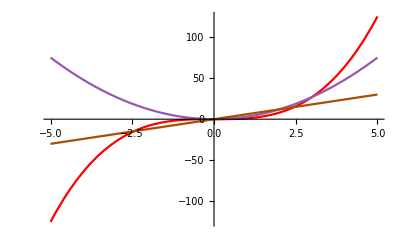

```mathematica
(*
Ex-58. Sketch the graph of f(x) = x^3, its first and second derivatives in one set of axes, for -5≤ x ≤ 5 in different color.
*)
f[x_]=x^3;
Plot[{f[x],f'[x],f''[x]},{x,-5,5},PlotStyle->{RGBColor[1,0,0],RGBColor[0.59,0.35,0.7],RGBColor[0.66,0.31,0.01]}]
```

```mathematica
(*
Ex-60. Compute the first 5 derivatives of 
i) f(x) = e^(x^2)
  ii) f(x) = sin 2x
    iii) f(x) = x^2 e^(2x) at x=0.
put the result in the tabular form.
*)
```

```mathematica
f[x_]=Exp[x^2];
Dtable = Table[{n,D[f[x],{x,n}]/.x-> 0},{n,1,5}];
TableForm[Dtable,TableAlignments->Center,TableDirections->Row,TableSpacing->2,TableHeadings->{None,{"n","f^(n)(0)"}}]
```

n | 1 | 2 | 3 | 4 | 5
f^(n)(0) | 0 | 2 | 0 | 12 | 0

```mathematica
(*
Ex-61. Sketch the graph and its tangent line of the function f(x)=sin x at x = Pi/3. 
*)
```



```mathematica
f[x_]=Sin[x];
a = Pi/3;
g[x_]=f[a]+f'[a](x-a);
Plot[{f[x],g(x)},{x,0,2*Pi}]
```

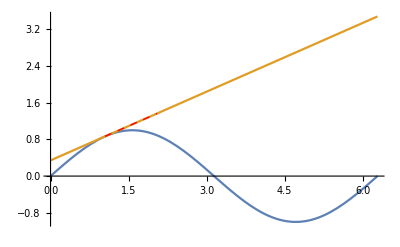

```mathematica
(*Now we draw a tangent line on the above curve
*)
Plot[{f[x],g[x]},{x,0,2*Pi},Epilog->{Red,Dashed,Line[{{a,f[a]},{a+1,g[a+1]}}]}]
```

```mathematica
(*
Ex-62. Sketch the spehere x^2+y^2+z^2=14 and its tangent at the point (1,2,3).
*)
```

```mathematica
f[x_,y_,z_]=x^2+y^2+z^2;
x0=1;y0=2;z0=3;
fx=Derivative[1,0,0][f][x0,y0,z0];
fy=Derivative[0,1,0][f][x0,y0,z0];
fz=Derivative[0,0,1][f][x0,y0,z0];
tp=(x-x0)*fx+(y-y0)*fy+(z-z0)*fz//Simplify
```

2 (-14+x+2 y+3 z)

```mathematica
ContourPlot3D[{x^2+y^2+z^2==0,2(-14+x+2 y+3 z)==0},{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

```mathematica
(*
Ex-65.
-Graphics-
*)
```

```mathematica
(**65 ->  i**)
f[x_,y_]=Log[x^2+y^2];
der1 = Limit[(f[x+h,y]-f[x,y])/h,h-> 0]
der2 = D[f[x,y],x]
der3 = Limit[(f[x,y+h]-f[x,y])/h,h-> 0]
der4 =D[f[x,y],y]
der1==der2
der3==der4
```

(2 x)/(x^2+y^2)

(2 x)/(x^2+y^2)

(2 y)/(x^2+y^2)

(2 y)/(x^2+y^2)

True

True

```mathematica
(**65 ->  ii**)
```

```mathematica
f[x_,y_]=x^2+2*x*y+y^2;

der1=Limit[(f[x+h,y]-f[x,y])/h,h->0]
der2=D[f[x,y],x]
der3=Limit[(f[x,y+h]-f[x,y])/h,h->0]
der4=D[f[x,y],y]

FullSimplify[der1]==FullSimplify[der2]
(*Output:True*)

FullSimplify[der3]==FullSimplify[der4]
(*Output:True*)
```

2 (x+y)

2 x+2 y

2 (x+y)

2 x+2 y

True

True

```mathematica
(*
Ex-66.
-Graphics-
*)
```

```mathematica
f[x_,y_]=(√(2x-y)-2)/(2x-y-4);
Subscript[f, x][x_,y_]=Limit[(f[x+h,y]-f[x,y])/h,h-> 0];
Subscript[f, y][x_,y_]=Limit[(f[x,y+k]-f[x,y])/k,k-> 0];
Subscript[f, xx][x_,y_]=Limit[(Subscript[f, x][x+h,y]-Subscript[f, x][x,y])/h,h-> 0];
Subscript[f, yy][x_,y_]=Limit[(Subscript[f, y][x,y+k]-Subscript[f, y][x,y])/k,k-> 0];
Subscript[f, xy][x_,y_]=Limit[(Subscript[f, x][x,y+k]-Subscript[f, x][x,y])/k,k-> 0];
Subscript[f, yx][x_,y_]=Limit[(Subscript[f, y][x+h,y]-Subscript[f, y][x,y])/h,h-> 0];
Subscript[f, x][2,0]
Subscript[f, y][2,0]
Subscript[f, xx][2,0]
Subscript[f, yy][2,0]
Subscript[f, xy][2,0]
Subscript[f, yx][2,0]
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

```mathematica
(*
Ex-67.

if u = sin^-1 (x+y)/(√x+√y), then write Mathematica code to show that x (∂u)/(∂x)+y (∂u)/(∂y)=1/2 tan u
*)
```

```mathematica
u=ArcSin[(x+y)/(Sqrt[x]+Sqrt[y])];

(*Calculate the derivatives and simplify the expression*)
eq=x*D[u,x]+y*D[u,y]==1/2*Tan[u]//FullSimplify
```

True

```mathematica
(*
Ex-69.
-Graphics-
*)
(*69-i*)
```

```mathematica
f[x_,y_]=x*Exp[x*y]
D[f[x,y],x]
```

ⅇ^(x y) x

ⅇ^(x y)+ⅇ^(x y) x y

```mathematica
D[f[x,y],y]
```

ⅇ^(x y) x^2

```mathematica
D[f[x,y],{x,2}]
```

2 ⅇ^(x y) y+ⅇ^(x y) x y^2

```mathematica
D[f[x,y],{y,2}]
```

ⅇ^(x y) x^3

```mathematica
(*69-ii*)
```

```mathematica
f[x_,y_]:=x^2*Exp[x*y];

(*Partial derivatives*)
fx[x_,y_]:=D[f[x,y],x];
fy[x_,y_]:=D[f[x,y],y];

(*Mixed partial derivatives*)
fxx[x_,y_]:=D[fx[x,y],x];
fyy[x_,y_]:=D[fy[x,y],y];
fxy[x_,y_]:=D[fx[x,y],y];
fyx[x_,y_]:=D[fy[x,y],x];

(*Display symbolic expressions*)
FullForm[fx[x,y]]
FullForm[fy[x,y]]
FullForm[fxx[x,y]]
FullForm[fyy[x,y]]
FullForm[fxy[x,y]]
FullForm[fyx[x,y]]
```

Plus[Times[2,Power[E,Times[x,y]],x],Times[Power[E,Times[x,y]],Power[x,2],y]]

Times[Power[E,Times[x,y]],Power[x,3]]

Plus[Times[2,Power[E,Times[x,y]]],Times[4,Power[E,Times[x,y]],x,y],Times[Power[E,Times[x,y]],Power[x,2],Power[y,2]]]

Times[Power[E,Times[x,y]],Power[x,4]]

Plus[Times[3,Power[E,Times[x,y]],Power[x,2]],Times[Power[E,Times[x,y]],Power[x,3],y]]

Plus[Times[3,Power[E,Times[x,y]],Power[x,2]],Times[Power[E,Times[x,y]],Power[x,3],y]]